```mathematica
1 qubit;

(* We evaluate: ;
   |0><0| -> p_{1} |0><0\  + p_{2} |1><1|  + p_{3} |x><x\ + p_{4}|y><y| 
  |1><1| -> p_{5} |0><0\  + p_{6} |1><1|  + p_{7} |x><x\ + p_{8}|y><y|
 |x><x| -> p_{9} |0><0\  + p_{10}|1><1|  + p_{11}|x><x\ + p_{12}|y><y|
|y><y| -> p_{13}|0><0\  + p_{14}|1><1|  + p_{15}|x><x\ + p_{16}|y><y|
*)

(* We can also parametrise as: ;
   |0><0| -> p_{0} |0><0\  + p_{1}|1><1|  + p_{2} |x><x\   + p_{3}|y><y| 
  |1><1| -> p_{4} |0><0\  + p_{0}|1><1|  + p_{5} |x><x\   + p_{6}|y><y|
 |x><x| -> p_{7} |0><0\  + p_{8}|1><1|  + p_{0} |x><x\   + p_{9}|y><y|
|y><y| -> p_{10}|0><0\  + p_{11}|1><1| + p_{12}|x><x\   + p_{0}|y><y|

This is the best one to use because in this way we are measuring wrt the probability of QPT being performed perfectly.

The ways we are giving values to these probabilities is like this

   p1=random val 1      =p4=p7=p10
    p2=random val 2      =p5=p8=p1
p3=random val 3      =p6=p9=p12
*)

Clear["`*"]
PM={{{1,0},{0,1}},{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}};
Id=PM[[1]];X=PM[[2]];Y=PM[[3]];Z=PM[[4]];
Sideal={{{1,0},{0,0}}, {{0,0},{0,1}},{{1,I},{-I,1}}/2,{{1,1},{1,1}}/2}; 
Pideal={{{1,0},{0,0}}, {{0,0},{0,1}},{{1,I},{-I,1}}/2,{{1,1},{1,1}}/2}; 

T={{Id.rho.Id,Id.rho.X, Id.rho.Y, Id.rho.Z, X.rho.Id,X.rho.X, X.rho.Y, X.rho.Z, Y.rho.Id,Y.rho.X, Y.rho.Y, Y.rho.Z, Z.rho.Id,Z.rho.X, Z.rho.Y, Z.rho.Z}};
T2={{Id1,Id2, Id3, Id4, X1,X2, X3, X4, Y1,Y2, Y3, Y4, Z1,Z2, Z3, Z4}};

CalculateAInverse[RP_, RS_]:=Module[{A,AM,AI},
A=Table[Tr[RP[[i]].PM[[p]].RS[[j]].PM[[q]]],{i,1,4},{j,1,4},{p,1,4},{q,1,4}];
AM=Partition[Flatten[A],{16}];
AI=Inverse[AM];
AI]

CalculateP[WP_,WS_,Gate_,Gate2_]:=Module[{pvertical},
pvertical =ArrayFlatten[Table[{Tr[WP[[i]].Gate.WS[[j]].Gate2]},{i,1,4},{j,1,4}],1];
pvertical]

CalculateChi[WP_,WS_,AI_,Gate_,Gate2_]:= Module[{p,Chi},
p=CalculateP[WP,WS,Gate,Gate2];
Chi = AI.p;
Chi]

ReconstructGate[Chi_,T_]:=
Sum[Chi[[i,1]]T[[1,i]],{i,1,16}];

(*Fidelity calculated by comparing Chi vs the Reconstructed Chi*)
FChi[Chiid_, Chirec_]:=Module[{Numerator, Denominator},
Numerator=Tr[Chirec.ConjugateTranspose[Chiid]];
Denominator=(Sqrt[Tr[(Chirec).ConjugateTranspose[Chirec]]Tr[(Chiid).ConjugateTranspose[Chiid]]]);
Numerator/Denominator];

CalculateFChi[Projectors_,States_,AI_,Gate_,Gate2_]:=Module[{Chi,RecGate,FidelityChi,idealChi},
Chi=CalculateChi[Projectors,States,AI,Gate,Gate2];
idealChi=CalculateChi[Pideal,Sideal,AI,Gate,Gate2];
FidelityChi=FChi[idealChi,Chi];
Simplify[FidelityChi]]

AI= CalculateAInverse[Pideal,Sideal];
ChiIdeal=CalculateChi[Pideal,Sideal,AI,X,Id];

FindASetOfProbabilitiesAndFidelity[Gate_,Gate2_,Number_]:=Module[{probabilitySet,probPermutations,probFidelity,eq,variable,chi},
probabilitySet=N[IntegerPartitions[10,{4}]*10^(-1)];
probPermutations={};probFidelity={};
Do[AppendTo[probPermutations,Permutations[i]];,{i,probabilitySet}];
probPermutations=Flatten[probPermutations,1];
variable=T2[[1,Number]];
Do[probability0=i[[1]];probability1=i[[2]];probability2=i[[3]];probability3=i[[4]];
chi=CalculateChi[Pideal,StatesE,AI,Gate,Gate2];
eq=ReconstructGate[chi,T2];
AppendTo[i,N[CalculateFChi[Pideal,StatesE,AI,Gate,Gate2]]];
AppendTo[i,Coefficient[eq,variable]];
AppendTo[probFidelity,i],{i,probPermutations}];
probFidelity];

States={{{probability0,0},{0,0}},{{0,0},{0,probability0}},{{probability0,I*probability0},{-I*probability0,probability0}}/2,{{probability0,probability0},{probability0,probability0}}/2};
Error={{{0,0},{0,probability1}}+{{probability2,I*probability2},{-I*probability2,probability2}}/2+{{probability3,probability3},{probability3,probability3}}/2,
{{probability4,0},{0,0}}+{{probability5,I*probability5},{-I*probability5,probability5}}/2+{{probability6,probability6},{probability6,probability6}}/2,{{probability7,0},{0,0}}+{{0,0},{0,probability8}}+{{probability9,probability9},{probability9,probability9}}/2,{{probability10,0},{0,0}}+{{0,0},{0,probability11}}+{{probability12,I*probability12},{-I*probability12,probability12}}/2};

probability4=probability1;
probability7=probability1;
probability10=probability1;

probability5=probability2;
probability8=probability2;
probability11=probability2;

probability6=probability3;
probability9=probability3;
probability12=probability3;

StatesE=States+Error;

RePlotResults[ProbabilitiesFidelities_,featureNumber_,String_]:=Module[{Plot},Plot=ListPlot[Table[{ProbabilitiesFidelities[[i,1]],Re[ProbabilitiesFidelities[[i,featureNumber]]]},{i,1,Length[ProbabilitiesFidelities]}]];
Show[Plot,AxesLabel->{HoldForm[Probability of correct input],HoldForm[Re[String]]},PlotLabel->HoldForm[Distribution of Re[String]],LabelStyle->{GrayLevel[0]}]];
ImPlotResults[ProbabilitiesFidelities_,featureNumber_,String_]:=Module[{Plot},Plot=ListPlot[Table[{ProbabilitiesFidelities[[i,1]],Im[ProbabilitiesFidelities[[i,featureNumber]]]},{i,1,Length[ProbabilitiesFidelities]}]];
Show[Plot,AxesLabel->{HoldForm[Probability of correct input],HoldForm[Im[String]]},PlotLabel->HoldForm[Distribution of Im[String]],LabelStyle->{GrayLevel[0]}]];
```

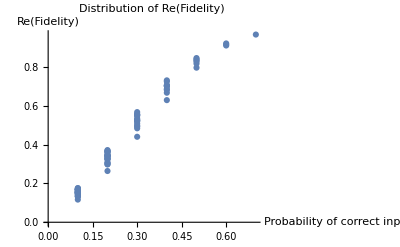

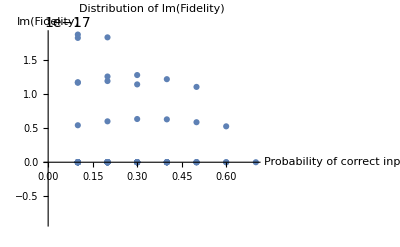

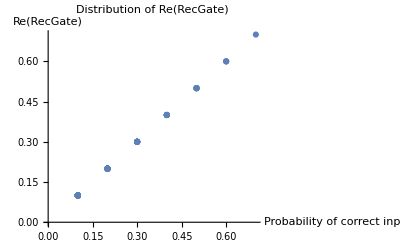

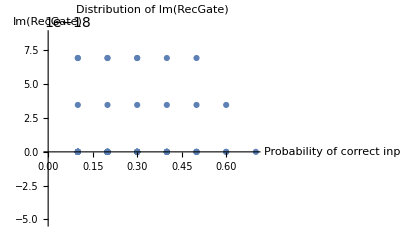

```mathematica
X gates;

Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[X,Id,5];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```

-Graphics-

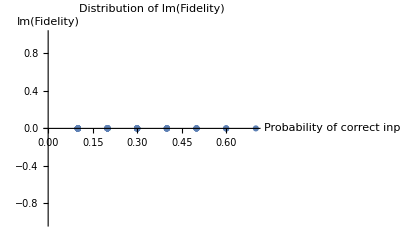

-Graphics-

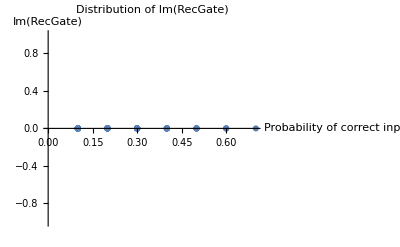

```mathematica
X.rho.X gate;

Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[X,X,6];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```

-Graphics-

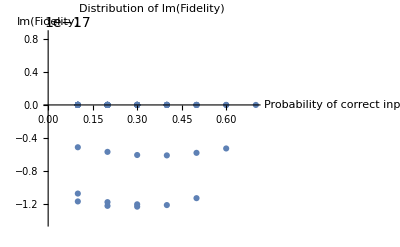

-Graphics-

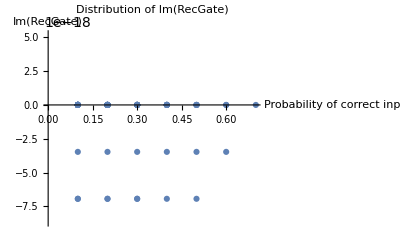

```mathematica
Y gates;

Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[Y,Id,9];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```

```mathematica
Y.rho.Y gates;

Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[Y,Y,11];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Z gates;

Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[Z,Id,13];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

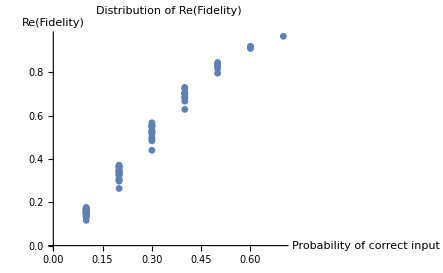

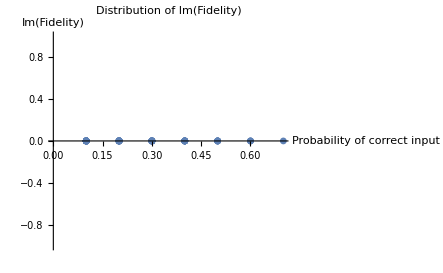

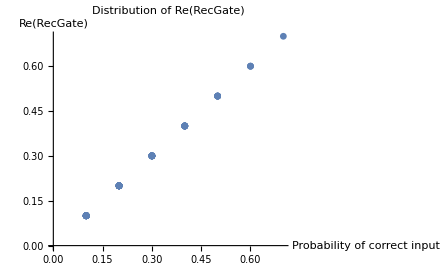

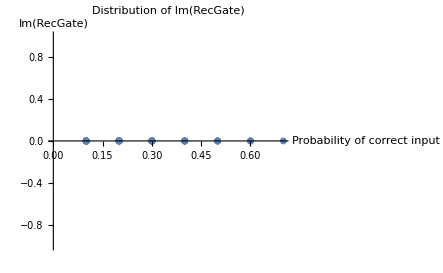

```mathematica
Z.rho.Z gates;
Clear[ProbabilitiesFidelities]
ProbabilitiesFidelities=FindASetOfProbabilitiesAndFidelity[Z,Z,16];
Do[ProbabilitiesFidelities=Delete[ProbabilitiesFidelities,{{i,2},{i,3},{i,4}}];,{i,1,Length[ProbabilitiesFidelities]}];
SortBy[ProbabilitiesFidelities,First]//MatrixForm;

RePlotResults[ProbabilitiesFidelities,2,"Fidelity"]
ImPlotResults[ProbabilitiesFidelities,2,"Fidelity"]
RePlotResults[ProbabilitiesFidelities,3,"RecGate"]
ImPlotResults[ProbabilitiesFidelities,3,"RecGate"]
```